```mathematica
Get["QuantumWalks`"]
```

```mathematica
(*2. Definir Parámetros del Estadio*)
L=1; (*Semilongitud recta*)
R=1; (*Radio*)
geometryData=GenerateFullStadiumBasis[L,R]; (*Generar geometría completa*)
```

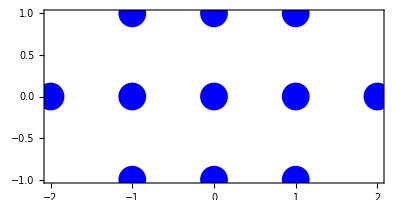

```mathematica
(*3. Construir Operadores*)
(*Aquí es donde usamos tu NUEVA funcionalidad para 4 estados*)
S=BuildShiftOperators[geometryData,CoinDimension->4];

(*Definir la Moneda de Grover 4x4*)
(*Difunde la amplitud equitativamente entre Arriba,Abajo,Der,Izq*)
groverMatrix=1/2*{{-1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}};

(*Expandir la moneda al espacio completo (Tensor Product implícito)*)
(*Usamos la función Coin existente en DQWL.wl*)
c=Coin[N@groverMatrix,geometryData["Dimension"]];

(*Operador de Evolución Unitaria*)
U=S.c;

ListPlot[geometryData["Coords"],PlotStyle->{PointSize[0.05],Blue},AspectRatio->Automatic,Frame->True]
```

```mathematica
U//Dimensions
```

{44,44}

```mathematica
eigenphases=Mod[Arg[Eigenvalues[U]],2Pi];
```

Eigenvalues::arh: Because finding 7876 out of the 7876 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

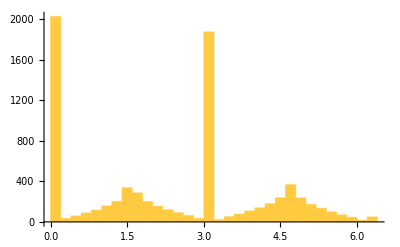

```mathematica
Histogram[eigenphases,Automatic,"Count"]
```

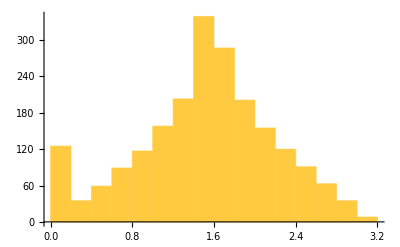

```mathematica
Histogram[Select[eigenphases,3.1415926535897927>#>0&],Automatic,"Count"]
```

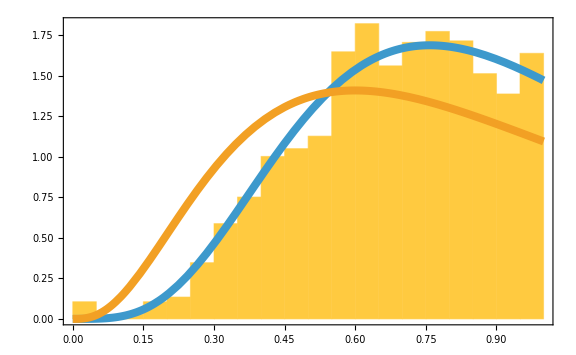

```mathematica
Show[
Histogram[NormalizedSpacingRatios[Select[eigenphases,3.1415926535897927>#>0&],4],Automatic,"PDF",Frame->True,FrameStyle->Directive[Black,25],FrameLabel->{"", ""},ImageSize->Large],
Plot[2*{RatiosDistribution[r,4],RatiosDistributionPoisson[r,4]}//Evaluate,{r,0,1},PlotLegends->Placed[{"",""}, {Left,Top}],LabelStyle->Directive[Black,25],PlotStyle->Directive[Thickness[0.01]]]
]
```

```mathematica
(*4. Definir Estado Inicial*)
(*Localizado en el centro (0,0) con superposición simétrica de direcciones*)
centerIdx=geometryData["Mapping"][{0,0}];
dimHilbert=4*geometryData["Dimension"];

psi0=SparseArray[{},dimHilbert];
(*Llenar los 4 estados internos del sitio central:4*(idx-1)+{1,2,3,4}*)
indicesMoneda=4*(centerIdx-1)+{1,2,3,4};
psi0[[indicesMoneda]]=1/2; (*Normalizado:Sqrt[1/4]^2*4=1*)

(*5. Evolución Temporal*)
timeSteps=30;
psiT=MatrixPower[U,timeSteps,psi0]; (*Evolución rápida con matrices dispersas*)

(*6. Visualización*)
(*Colapsar los grados de libertad de la moneda para obtener densidad de probabilidad*)
probDensity=Total[Partition[Abs[psiT]^2,4],{2}];

(*Crear datos para graficar:{x,y,probabilidad}*)
plotData=MapThread[Append,{geometryData["Coords"],probDensity}];

(*Graficar*)
ListDensityPlot[plotData,PlotLabel->Row[{"Densidad de Probabilidad @ t = ",timeSteps}],ColorFunction->"SunsetColors",PlotRange->All,AspectRatio->Automatic,ImageSize->Medium,Epilog->{White,Dashed,Circle[{0,0},R],Line[{{-L,-R},{L,-R}}],Line[{{-L,R},{L,R}}]} (*Dibuja el contorno del estadio*)]
```

## Symmetrized version

```mathematica
(*---1. Generador de Operadores de Paridad (Px,Py)---*)
GetSymmetryOperators[gridData_Association]:=Module[{coords,map,dim,permX,permY,coinPx,coinPy,Px,Py},coords=gridData["Coords"];
map=gridData["Mapping"];
dim=gridData["Dimension"];
(*1. Mapeos de Coordenadas*)(*Px:Reflexión especular respecto al eje Y (x->-x)*)permX=Lookup[map,{-1,1}*#&/@coords];
(*Py:Reflexión especular respecto al eje X (y->-y)*)permY=Lookup[map,{1,-1}*#&/@coords];
(*Validación básica*)If[AnyTrue[permX,MissingQ]||AnyTrue[permY,MissingQ],Print["Error: La geometría no es simétrica respecto a los ejes."];
Return[$Failed];];
(*2. Acción sobre la Moneda (4 estados)*)(*Índices:1:Up,2:Down,3:Right,4:Left*)(*Px Coin:x->-x.Invierte direcciones horizontales (Right<->Left).Verticales quietas.*)coinPx=SparseArray[{{1,1}->1,{2,2}->1,{3,4}->1,{4,3}->1},{4,4}];
(*Py Coin:y->-y.Invierte direcciones verticales (Up<->Down).Horizontales quietas.*)coinPy=SparseArray[{{1,2}->1,{2,1}->1,{3,3}->1,{4,4}->1},{4,4}];
(*3. Construcción Tensorial (Posición x Moneda)*)(*Px*)Px=SparseArray[Flatten@Table[Module[{targetSite=permX[[site]]},(*Mover bloque de moneda completo de'site' a'targetSite' transformado*)Table[{4*(targetSite-1)+r,4*(site-1)+c}->coinPx[[r,c]],{r,1,4},{c,1,4}]],{site,1,dim}],{4*dim,4*dim}];
(*Py*)Py=SparseArray[Flatten@Table[Module[{targetSite=permY[[site]]},Table[{4*(targetSite-1)+r,4*(site-1)+c}->coinPy[[r,c]],{r,1,4},{c,1,4}]],{site,1,dim}],{4*dim,4*dim}];
{Px,Py}];

GetSectorHamiltonian[U_SparseArray,Px_SparseArray,Py_SparseArray,sector_String]:=Module[{dimFull=Length[U],Id,Projector,(*Variables para descomposición*)basisVectors,Ureduced,tol=10^-5 (*Tolerancia para distinguir 0 de algo real*)},Id=IdentityMatrix[dimFull,SparseArray];
(*1. Construir el Proyector Algebraico*)Projector=Switch[sector,"A1",0.25*(Id+Px).(Id+Py),"A2",0.25*(Id-Px).(Id-Py),"B1",0.25*(Id+Px).(Id-Py),"B2",0.25*(Id-Px).(Id+Py)];
(*2. Extracción Robusta de la Base (Fix para Puntos en Ejes)*)(*Usamos la propiedad:Los vectores base son los eigenvectores del Proyector con valor 1.*)(*Dado que P^2=P,los valores singulares son 1 o 0.*)(*Estrategia optimizada para Sparse:Tomamos columnas no triviales y ortogonalizamos con tolerancia estricta.*)basisVectors=Select[Orthogonalize[(*Solo intentamos ortogonalizar columnas que ya tengan norma decente*)Select[Transpose[Normal[Projector]],Norm[#]>tol&],Method->"Householder",(*Más estable que Gram-Schmidt*)Tolerance->tol],(*Filtro final:Asegurar que el resultado de ortogonalizar no sea cero*)Norm[#]>tol&];
(*Validación de Dimensión*)If[Length[basisVectors]==0,Print["Advertencia: El sector ",sector," está vacío."];
Return[$Failed]];
(*3. Proyección*)(*V es la matriz isometría N_total x N_sector*)V=SparseArray[Transpose[basisVectors]];
Ureduced=Chop[ConjugateTranspose[V].U.V];
(*Retornamos también la dimensión para que verifiques la suma*)Print["Sector ",sector," -> Dimensión: ",Length[basisVectors]];
Ureduced];
```

```mathematica
(*---TEST---*)(*1. Generar Sistema*)
L=13;R=13;
geo=GenerateFullStadiumBasis[L,R];
Sop=BuildShiftOperators[geo,CoinDimension->4];
CoinOp=Coin[1/2*{{-1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}},geo["Dimension"]];
Ufull=Sop.CoinOp;

(*2. Obtener Operadores de Simetría*)
{Px,Py}=GetSymmetryOperators[geo];

(*3. Obtener U en el sector A1 (Totalmente Simétrico)*)
UA1=Chop@GetSectorHamiltonian[Ufull,Px,Py,"A1"];

(*4. Verificaciones*)
Print["Unitariedad del sector A1: ",UnitaryMatrixQ[UA1]];
Print["Dimensiones Full: ",Dimensions[Ufull]];
Print["Dimensiones A1:   ",Dimensions[UA1]];

(*5. Espectro (Eigenfases)*)
eigenvaluesA1=Eigenvalues[Normal@Chop@N@UA1];
eigenphasesA1=Arg[eigenvaluesA1];
```

Sector A1 -> Dimensión: 1295

Unitariedad del sector A1: True

Dimensiones Full: {5020,5020}

Dimensiones A1:   {1295,1295}

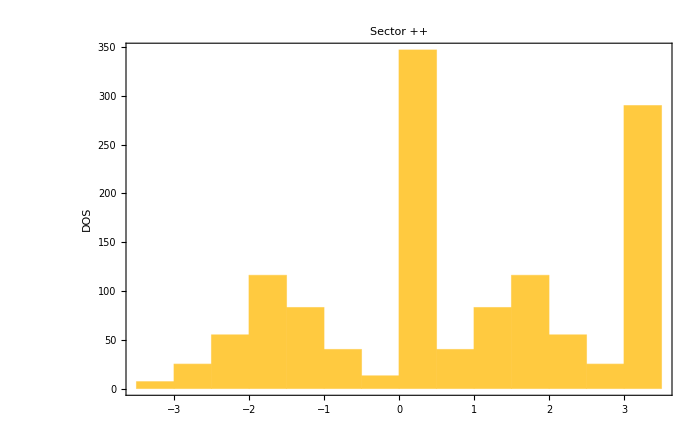

```mathematica
Histogram[eigenphasesA1,Automatic,"Count",PlotLabel->"Sector ++",Frame->True,FrameStyle->Directive[Black,27],LabelStyle->Directive[Black,27],FrameLabel->{"","DOS"},ImageSize->700]
```

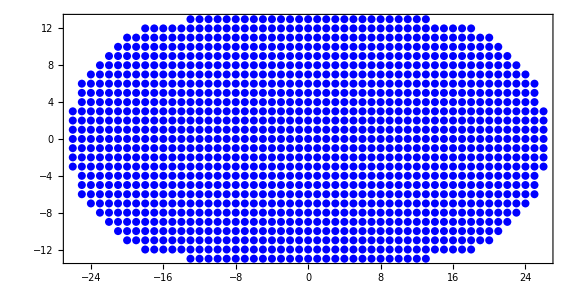

```mathematica
geo=GenerateFullStadiumBasis[L,R];
ListPlot[geo["Coords"],PlotStyle->{PointSize[0.01],Blue},AspectRatio->Automatic,Frame->True,ImageSize->Large,FrameStyle->Directive[Black,27]]
```

### Estadística espectral de Ufull

```mathematica
eigenvalues=Eigenvalues[Normal@Chop@N@Ufull];
eigenphases=Arg[eigenvalues];
```

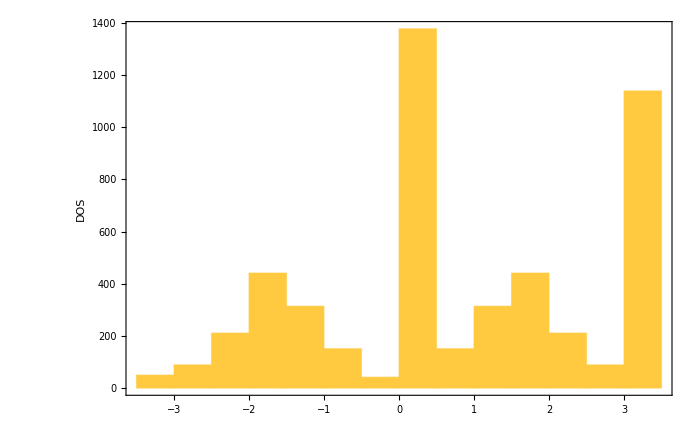

```mathematica
Histogram[Chop@eigenphases,Automatic,"Count",Frame->True,FrameStyle->Directive[Black,30],LabelStyle->Directive[Black,30],FrameLabel->{"","DOS"},ImageSize->700]
```

```mathematica
Select[Tally[Chop@eigenphases],#[[2]]>1&]
```

{{3.14159,1132},{0,1335},{-3.14159,43}}

```mathematica
HistogramList[Chop@eigenphases]
```

{{-7/2,-3,-5/2,-2,-3/2,-1,-1/2,0,1/2,1,3/2,2,5/2,3,7/2},{50,89,211,441,314,151,42,1377,151,314,441,211,89,1139}}

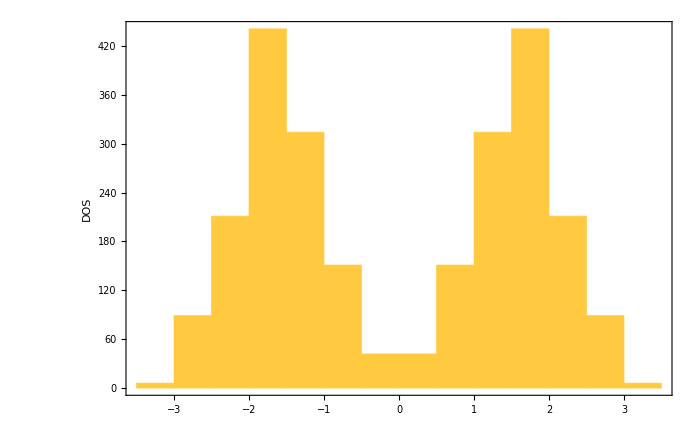

```mathematica
filteredEigenphases=Select[Chop@eigenphases,-Pi<#<0||0<#<Pi&];
Histogram[filteredEigenphases,Automatic,"Count",Frame->True,FrameStyle->Directive[Black,30],LabelStyle->Directive[Black,30],FrameLabel->{"","DOS"},ImageSize->700]
```

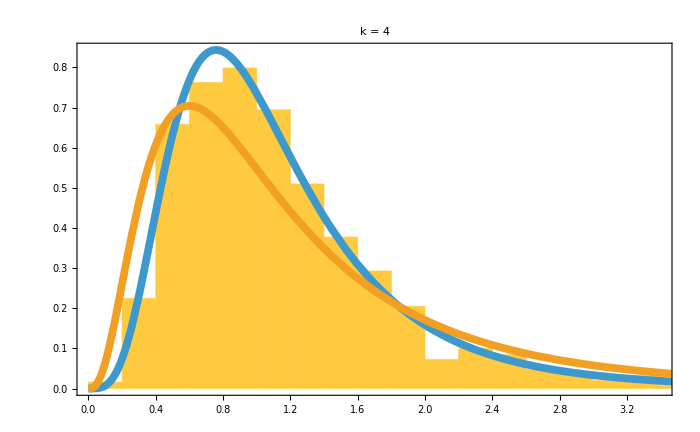

```mathematica
k=4;
Show[
Histogram[SpacingRatios[filteredEigenphases,k],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,32],ImageSize->700,PlotLabel->"k = "<>ToString[k],LabelStyle->Directive[Black,25]],
Plot[{RatiosDistribution[r,k],RatiosDistributionPoisson[r,k]},{r,0,15},PlotRange->All,PlotStyle->{Directive[Thickness[0.008]]},PlotLegends->Placed[{"",""},{Right,Top}],LabelStyle->Directive[Black,34]]
]
```

```mathematica
Table[{EmpiricalKLDivergence[SpacingRatios[filteredEigenphases,k],RatiosDistribution[#,k]&,{0,10,1.}],
EmpiricalKLDivergence[SpacingRatios[filteredEigenphases,k],RatiosDistributionPoisson[#,k]&]}
,{k,4}]
```

{{0.0369661,0.126923},{0.0374791,0.0505164},{0.0205787,0.0533924},{0.019493,0.0938074}}

```mathematica
?EmpiricalKLDivergence
```

### Estadística espectral

```mathematica
<<QMB`
```

```mathematica
Select[Tally[eigenphasesA1],#[[2]]>1&]
```

{{0.,314},{3.14159,285},{-3.14159,9}}

```mathematica
cleanEigenphases=Select[eigenphasesA1,-Pi<#<0&];
```

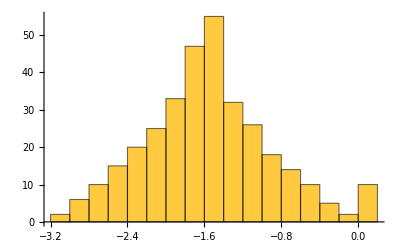

```mathematica
Histogram[cleanEigenphases,Automatic,"Count"]
```

0.166449

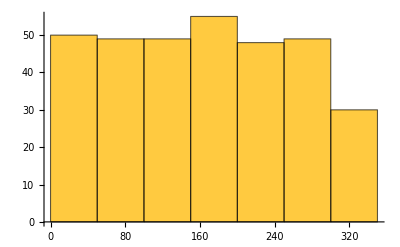

```mathematica
Unfold[cleanEigenphases]["Bandwidth"]
Histogram[unfolded=Unfold[cleanEigenphases,"Bandwidth"->0.1]["UnfoldedLevels"],Automatic,"Count"]
```

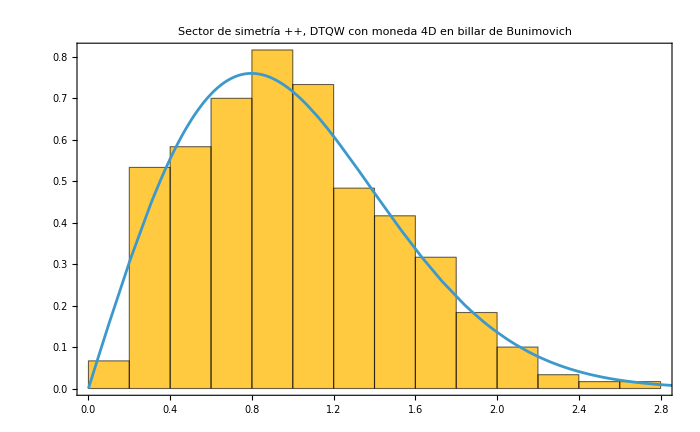

```mathematica
Show[
Histogram[Differences[unfolded[[;;-30]]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,27],ImageSize->700,PlotLabel->"Sector de simetría ++, \n DTQW con moneda 4D en billar de Bunimovich",LabelStyle->Directive[Black,22]],
Plot[PDF[RayleighDistribution[Sqrt[2/Pi]],s],{s,0,5}]
]
```

### Rectángulo

```mathematica
(*---TEST---*)(*1. Generar Sistema*)
L=40;R=20;
geo=GenerateRectangleBasis[L,R];
Sop=BuildShiftOperators[geo,CoinDimension->4];
CoinOp=Coin[1/2*{{-1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}},geo["Dimension"]];
Ufull=Sop.CoinOp;
```

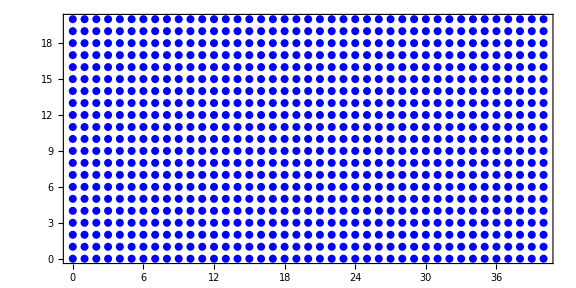

```mathematica
ListPlot[geo["Coords"],PlotStyle->{PointSize[0.01],Blue},AspectRatio->Automatic,Frame->True,ImageSize->Large]
```

### Estadística espectral

```mathematica
<<QMB`
```

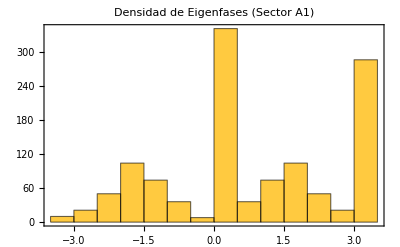

```mathematica
evals=Eigenvalues[Normal@Chop@N@Ufull];eigenphases=Arg[evals];

Histogram[eigenphasesA1,Automatic,"Count",PlotLabel->"Densidad de Eigenfases (Sector A1)",Frame->True]
```

```mathematica
Select[Tally[eigenphases],#[[2]]>1&]
```

{{3.14159,726},{0.,835},{-3.14159,47},{3.14159,26},{-3.14159,2}}

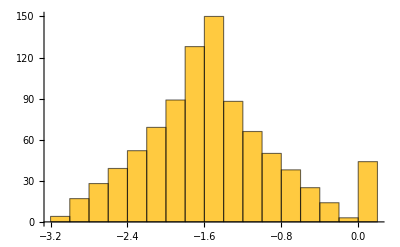

```mathematica
cleanEigenphases=Select[eigenphases,-Pi<#<0&];
Histogram[cleanEigenphases,Automatic,"Count"]
```

0.137123

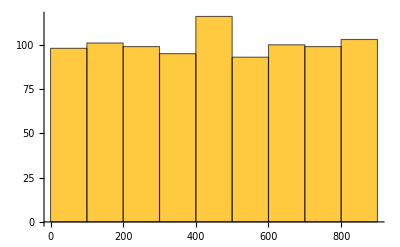

```mathematica
Unfold[cleanEigenphases]["Bandwidth"]
Histogram[unfolded=Unfold[cleanEigenphases,"Bandwidth"->0.08]["UnfoldedLevels"],Automatic,"Count"]
```

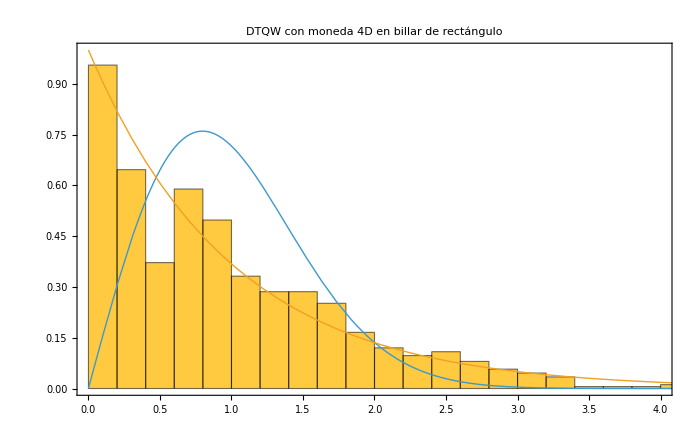

```mathematica
Show[
Histogram[Differences[unfolded[[;;-30]]],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,27],ImageSize->700,PlotLabel->"DTQW con moneda 4D en billar de rectángulo",LabelStyle->Directive[Black,22]],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,5},PlotStyle->{Directive[Thick],Directive[Thick]}]
]
```

## Nuevo gemini

```mathematica
c={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
g=1/2*{{-1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}};
```

```mathematica
MatrixForm/@{g,c.g.c}
```

{(-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2),(-1/2 | 1/2 | 1/2 | 1/2
1/2 | -1/2 | 1/2 | 1/2
1/2 | 1/2 | -1/2 | 1/2
1/2 | 1/2 | 1/2 | -1/2)}

```mathematica
L=20;R=20;
grid=GenerateFullStadiumBasis[L,R];
dimTotal=grid["Dimension"]
```

2933

```mathematica
<<QuantumWalks`
```

SetDelayed::write: Tag Integer in 25[θ_,θa_,θb_] is Protected.

```mathematica
(*Generar Sistema*)
grid=GenerateFullStadiumBasis[L,R];
dimTotal=4*grid["Dimension"];

(*Construir U total*)
Sop=BuildShiftOperators[grid,CoinDimension->4];
CoinOp=Coin[1/2*{{-1,1,1,1},{1,-1,1,1},{1,1,-1,1},{1,1,1,-1}},grid["Dimension"]];
Ufull=Sop.CoinOp;

(*Verificar Sectores*)
dimSum=0;
Do[Vsec=GetSymmetrySectorBasis[grid,s];
d=Last[Dimensions[Vsec]];
dimSum+=d;
(*Proyectar*)Usec=Chop[ConjugateTranspose[Vsec].Ufull.Vsec];
Print["Sector ",s," -> Dim: ",d," | Unitario? ",UnitaryMatrixQ[Usec]];,{s,{"A1","A2","B1","B2"}}];

Print["------------------"];
Print["Total Sistema: ",dimTotal];
Print["Suma Sectores: ",dimSum];
```

Sector A1 -> Dim: 2994 | Unitario? True

Sector A2 -> Dim: 2872 | Unitario? True

Sector B1 -> Dim: 2913 | Unitario? True

Sector B2 -> Dim: 2953 | Unitario? True

------------------

Total Sistema: 11732

Suma Sectores: 11732

Start

```mathematica
{evals,evecs}=Eigensystem[Normal@N@Ufull];
```

```mathematica
PlotStadiumEigenvector[eigenVector_?VectorQ,gridData_Association,opts:OptionsPattern[]]:=Module[{L,R,probDensity,plotData,boundaryGraphic,stadiumRegionCondition},(*1. Extraer parámetros geométricos*)L=gridData["Params"]["L"];
R=gridData["Params"]["R"];
(*2. Definir la condición de región (Matemática exacta del estadio)*)(*Un punto está dentro si su distancia al segmento central es<=R*)stadiumRegionCondition=Function[{x,y,z},RegionDistance[Line[{{-L,0},{L,0}}],{x,y}]<=R+0.1 (*Pequeño margen para el borde*)];
(*3. Calcular Densidad de Probabilidad Local*)(*Suma|c_i|^2 sobre los 4 estados de la moneda en cada sitio*)probDensity=Total[Partition[Abs[eigenVector]^2,4],{2}];
(*4. Fusionar Coordenadas con Probabilidad:{x,y,P}*)plotData=MapThread[Append,{gridData["Coords"],probDensity}];
(*5. Gráfico del Contorno (Decoración visual)*)boundaryGraphic={Directive[White,Dashed,Thick,Opacity[0.5]],Line[{{-L,R},{L,R}}],Line[{{-L,-R},{L,-R}}],Circle[{-L,0},R,{Pi/2,3Pi/2}],Circle[{L,0},R,{-Pi/2,Pi/2}]};
(*6. Generar Plot con Recorte*)ListDensityPlot[plotData,(*RegionFunction recorta el dibujo.Todo lo de fuera será del color del Background*)RegionFunction->stadiumRegionCondition,ColorFunction->"SunsetColors",PlotRange->{0,All},(*Asegura que 0 sea negro/oscuro*)Background->Black,(*El área fuera de la región será negra*)AspectRatio->Automatic,ImageSize->Large,Epilog->boundaryGraphic,Frame->False,Axes->False,PlotLabel->Style["Densidad de Probabilidad |ψ(x,y)|^2",White,15],(*Permite pasar opciones adicionales al llamar a la función*)FilterRules[{opts},Options[ListDensityPlot]]]]
```

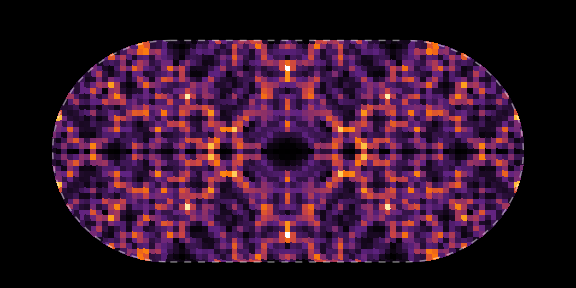
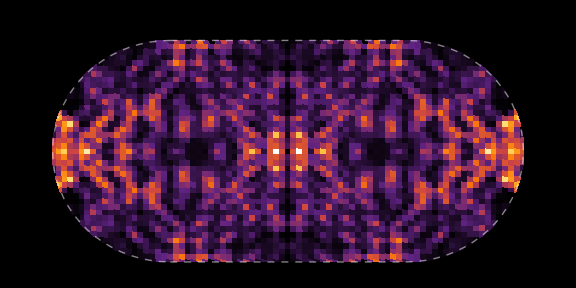
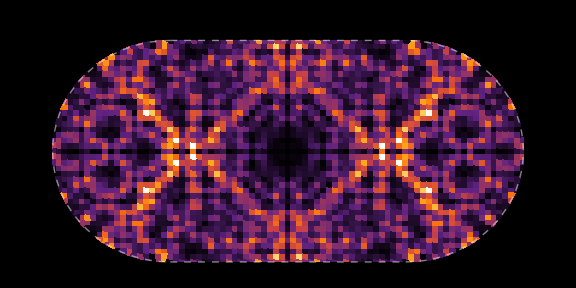
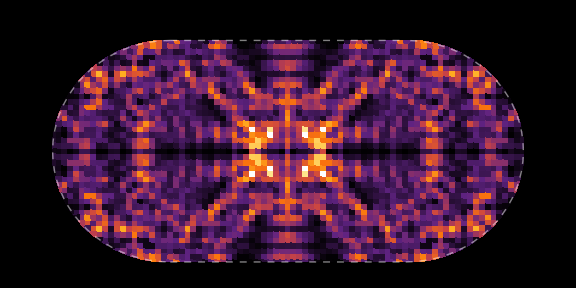
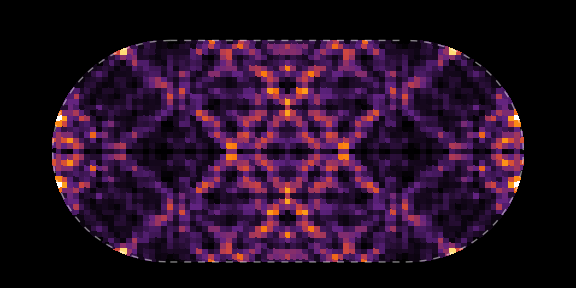
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotStadiumEigenvector[evecs[[#]],grid,InterpolationOrder->0]&/@Range[10]
```

8947

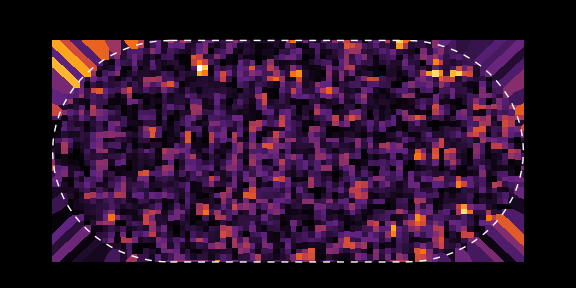
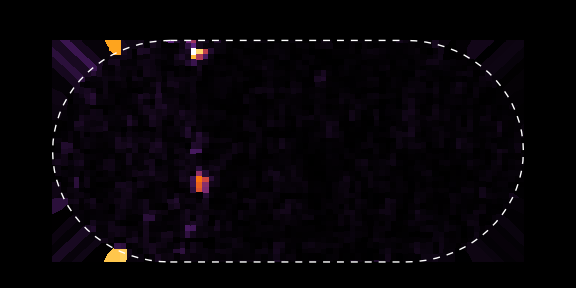
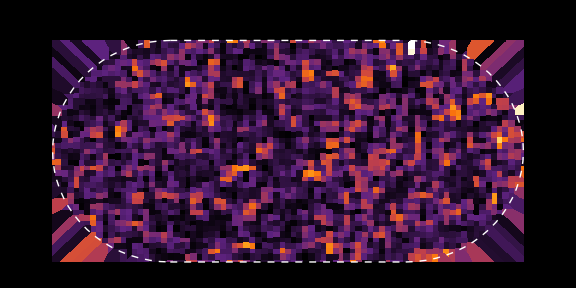
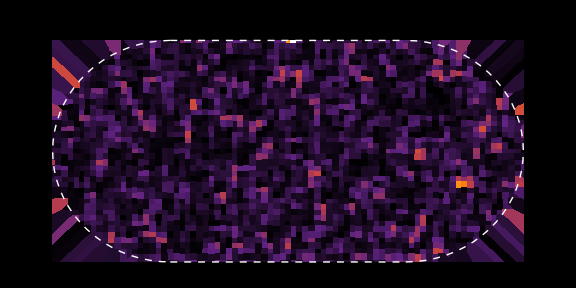
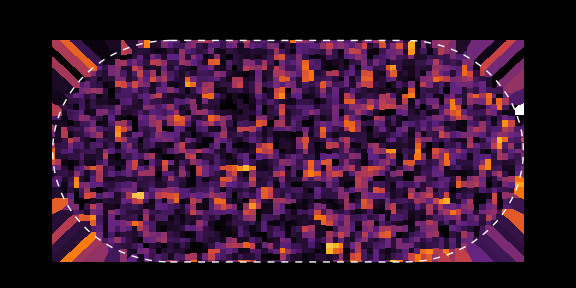
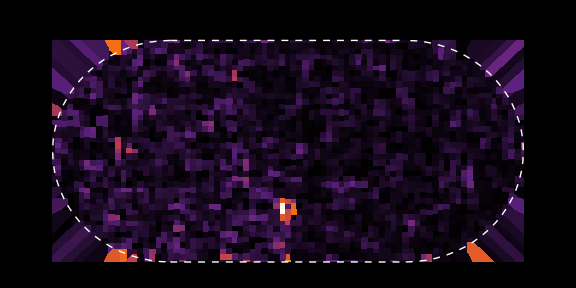
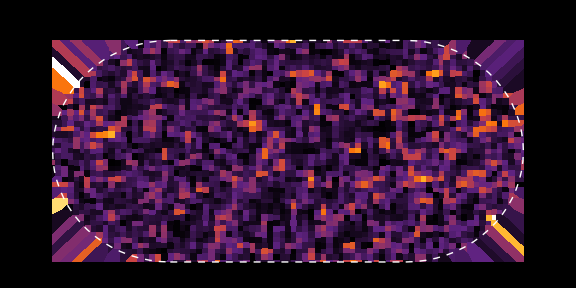
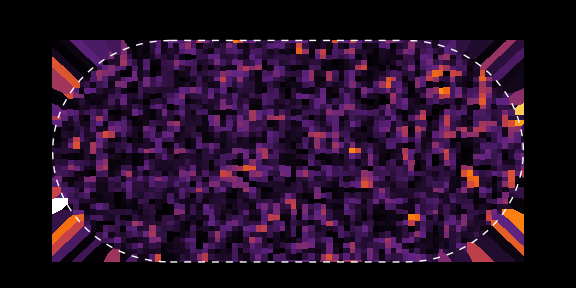
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
x=RandomChoice[Flatten[Position[Chop@Arg[evals],0]]]
PlotStadiumEigenvector[evecs[[#]],grid,InterpolationOrder->0]&/@Flatten[Position[Chop@Arg[evals],0]][[61;;80]]
```

End

```mathematica
eigenphases=Arg[Chop[Eigenvalues[Usec]]];
```

Eigenvalues::arh: Because finding 10499 out of the 10499 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

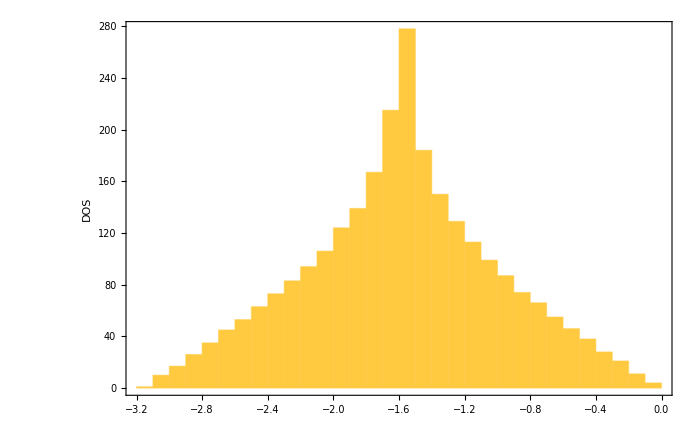

```mathematica
filteredEigenphases=Select[Chop@eigenphases,-Pi<#<0&];
Histogram[filteredEigenphases,Automatic,"Count",Frame->True,FrameStyle->Directive[Black,30],LabelStyle->Directive[Black,30],FrameLabel->{"","DOS"},ImageSize->700]
```

0.103107

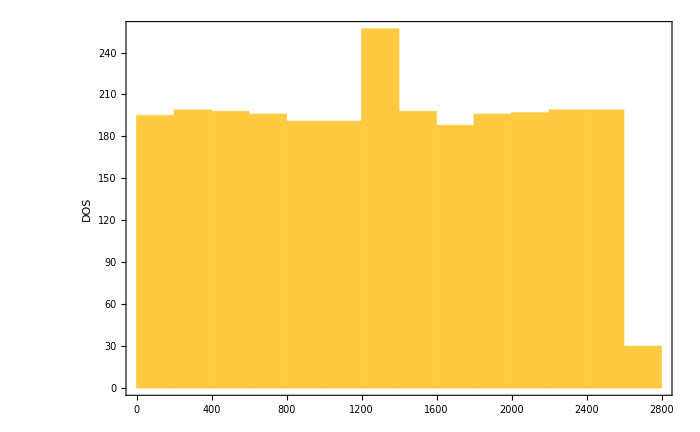

```mathematica
Unfold[filteredEigenphases]["Bandwidth"]
unfolded=Unfold[filteredEigenphases,"Bandwidth"->0.1]["UnfoldedLevels"];
Histogram[unfolded,Automatic,"Count",Frame->True,FrameStyle->Directive[Black,30],
LabelStyle->Directive[Black,30],FrameLabel->{"","DOS"},ImageSize->700]
```

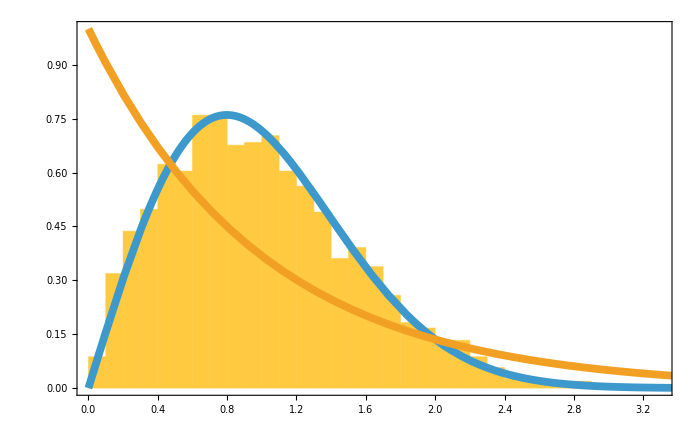

```mathematica
Show[
Histogram[Differences[unfolded],Automatic,"PDF",Frame->True,FrameLabel->{"", ""},FrameStyle->Directive[Black,32],ImageSize->700,LabelStyle->Directive[Black,25]],
Plot[{PDF[RayleighDistribution[Sqrt[2/Pi]],s],Exp[-s]},{s,0,5},PlotRange->All,PlotStyle->{Directive[Thickness[0.008]]},PlotLegends->Placed[{"",""},{Right,Top}],LabelStyle->Directive[Black,34]]
]
```